```mathematica
ZTransform[()^n *UnitStep[n-1],n,z]
```

0

```mathematica
InverseZTransform[z/(z-a),z,n]
```

a^n

```mathematica
ZTransform[-a^n*UnitStep[-n-1],n,z,GenerateConditions->True]
```

0

```mathematica
5/18
a=1.4
```

5/18

```mathematica
N[5/18]
```

0.277778

```mathematica
F=ZTransform[ 2*(1/3)^n UnitStep[n],n,z,GenerateConditions->True]
```

ConditionalExpression[(6 z)/(-1+3 z),Abs[z]>1/3]

```mathematica
F=ConditionalExpression[(3-5/6 z^-1)/((1-1/4 z^-1)(1-1/3 z^-1)),Abs[z]>1/4]
```

```mathematica
ConditionalExpression[(3-5/(6 z))/((1-1/(3 z)) (1-1/(4 z))),Abs[z]<1/3]
```

```mathematica
F=ConditionalExpression[(3-5/(6 z))/((1-1/(3 z)) (1-1/(4 z))),Abs[z]<1/3]
```

ConditionalExpression[(3-5/(6 z))/((1-1/(3 z)) (1-1/(4 z))),Abs[z]<1/3]

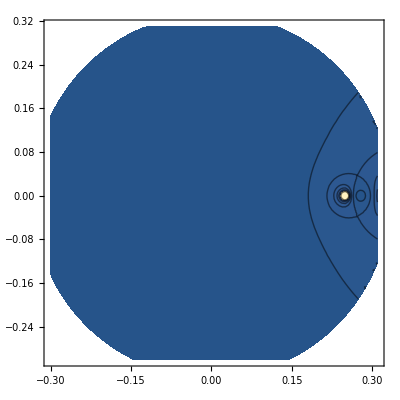
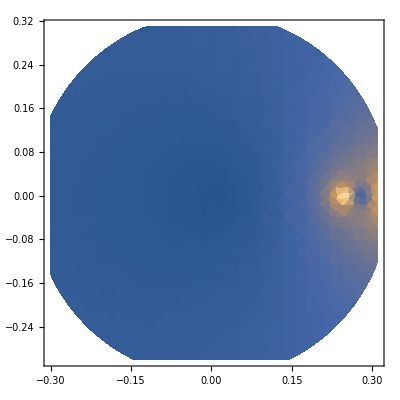
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{z=σ+I ω},Table[plot[Abs[F],{σ,-0.3,0.31},{ω,-0.3,0.31},PlotRange->All],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```

```mathematica
InverseZTransform[(1/3*z^-1/(1-1/2 z^-1)),z,n]
```

1/3 2^(1-n) UnitStep[-1+n]

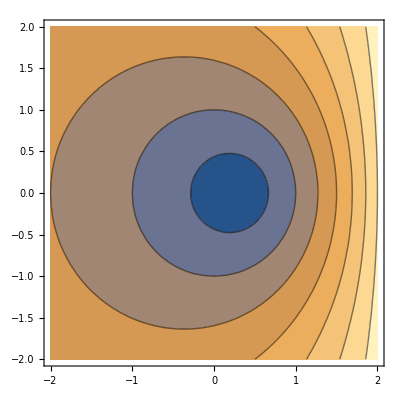
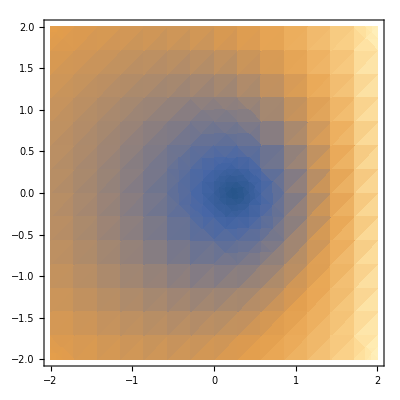
{-Graphics3D-,-Graphics-,-Graphics-}

```mathematica
Block[{z=σ+I ω},Table[plot[Abs[(1-4z)/(z-4)],{σ,-2,2},{ω,-2,2},PlotRange->Automatic],{plot,{Plot3D,ContourPlot,DensityPlot}}]]
```

```mathematica
z=σ+I ω
```

σ+ⅈ ω

```mathematica
Plot1=Plot3D[{Abs[(1-4z)/(z-4)]},{σ,-4,4},{ω,-4,4},ViewProjection->"Perspective"];
```

```mathematica
Plot2=ContourPlot3D[σ^2+ω^2==1,{σ,-4,4},{ω,-4,4},{t,-4,4},Mesh->None,ContourStyle->Directive[Red,Opacity[0.6],Specularity[White,30]]];
```

```mathematica
l1=Show[Plot1,Plot2]
```

-Graphics3D-